```mathematica
(*check basis transformation*)
ClearAll["Global`*"]
$Assumptions={x∈Reals && y∈Reals && a∈Reals};
```

```mathematica
U1= MatrixExp[-ⅈ*β/2*PauliMatrix[2]];
U1Dag= MatrixExp[ⅈ*β/2*PauliMatrix[2]];
FullSimplify[U1.PauliMatrix[1].U1Dag]//MatrixForm
```

```mathematica
(*test linearity*)
U1= MatrixExp[-ⅈ*(c*PauliMatrix[2]+d*PauliMatrix[3])];
U1Dag= MatrixExp[ⅈ*(c*PauliMatrix[2]+d*PauliMatrix[3])];
Op=a*PauliMatrix[1]+b*PauliMatrix[3];
Op0=a*PauliMatrix[1];
Op1=b*PauliMatrix[3];
X=FullSimplify[U1.Op0.U1Dag];
Y=FullSimplify[U1.Op1.U1Dag];
Z=FullSimplify[U1.Op.U1Dag];
ZZ=FullSimplify[X+Y];
Z==ZZ/.{a->1.8, b->1+0.3ⅈ,c->1.2,d->0.9}
```

```mathematica
(*******************************************************************************************************)
(*******************************************************************************************************)
(*Script starts here*)
ClearAll["Global`*"]
$Assumptions={ω∈Reals && ω1∈Reals && β∈Reals&& ωL∈Reals&& t∈Reals && t>0&&Ω∈Reals};

(*Hamiltonian in the lab frame, H0 (H1) is nuclear spin Hamiltonian in electron spin-0 (electron spin-1) subspace, Hd denotes driving field*)
H0=ωL/2*PauliMatrix[3]+Ω*Cos[ω*t +ϕ]*PauliMatrix[1];
H1=ω1/2*(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])+Ω*Cos[β]*Cos[ω*t +ϕ]*(Cos[β]*PauliMatrix[1]-Sin[β]*PauliMatrix[3])+Ω*Sin[β]*Cos[ω*t +ϕ]*(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3]);
(*unitary transformation*)
U=MatrixExp[ⅈ*ω/2*t(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])];
UDag =MatrixExp[-ⅈ*ω/2*t(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])];
```

```mathematica
(*******************************************************************************************************)
(*Check numerically for unitarity of transformation, it took too long analytically*)
Transpose[Conjugate[U]].U/.{ω->435, β->0.3,t->1.7,ωL->0.9, Ω->1,ϕ->π,ω1-> 563}//MatrixForm
(*******************************************************************************************************)
```

(1.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.+0. ⅈ)

```mathematica
H0Tilde0=FullSimplify[U.H0.UDag];
H1Tilde0=FullSimplify[U.H1.UDag];
H0Tilde= H0Tilde0-ω/2(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])//TrigExpand;
H1Tilde=H1Tilde0-ω/2(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])//TrigExpand;
```

```mathematica
(*Notiz aus dem Gespräch mit Guido: ich muss ja im Prinzip nicht in den rotierenden Rahmen gehen. Nur: dann wird die Integration vermutlich schwierig, weil es dann sehr schnell oszilliert*)
H0Tilde=H0Tilde/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H1Tilde=H1Tilde/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H0Tilde=FullSimplify[H0Tilde];
H1Tilde=FullSimplify[H1Tilde];
```

```mathematica
H0Tilde//MatrixForm
H1Tilde// MatrixForm
```

(((A-ωL) (A^2 ω+B^2 ω+A (-2 ω+√(B^2+(A-ωL)^2)) ωL+(ω-√(B^2+(A-ωL)^2)) ωL^2)+B √(B^2+(A-ωL)^2) (Ω (A-ωL) Cos[ϕ]+B ωL Cos[t ω]+Ω (A-ωL) (-2 Cos[ϕ+t ω]+Cos[ϕ+2 t ω])))/(2 (B^2+(A-ωL)^2)^(3/2)) | (-B ω √(B^2+(A-ωL)^2)+B (A-ωL) ωL (-1+Cos[t ω])+2 B^2 Ω Cos[ϕ+t ω]+Ω (A-ωL)^2 Cos[ϕ+2 t ω]-ⅈ B √(B^2+(A-ωL)^2) ωL Sin[t ω]+2 ⅈ A Ω √(B^2+(A-ωL)^2) Sin[ϕ] Sin[t ω]^2-2 ⅈ Ω √(B^2+(A-ωL)^2) ωL Sin[ϕ] Sin[t ω]^2+Ω (A-ωL) Cos[ϕ] (A-ωL-ⅈ √(B^2+(A-ωL)^2) Sin[2 t ω]))/(2 (B^2+(A-ωL)^2))
(-B ω √(B^2+(A-ωL)^2)+B (A-ωL) ωL (-1+Cos[t ω])+2 B^2 Ω Cos[ϕ+t ω]+Ω (A-ωL)^2 Cos[ϕ+2 t ω]+ⅈ B √(B^2+(A-ωL)^2) ωL Sin[t ω]-2 ⅈ A Ω √(B^2+(A-ωL)^2) Sin[ϕ] Sin[t ω]^2+2 ⅈ Ω √(B^2+(A-ωL)^2) ωL Sin[ϕ] Sin[t ω]^2+Ω (A-ωL) Cos[ϕ] (A-ωL+ⅈ √(B^2+(A-ωL)^2) Sin[2 t ω]))/(2 (B^2+(A-ωL)^2)) | -(B^2 ωL Cos[t ω]+(A-ωL) (ω √(B^2+(A-ωL)^2)+(A-ωL) ωL-4 B Ω Cos[ϕ+t ω] Sin[(t ω)/2]^2))/(2 (B^2+(A-ωL)^2)))

(-((A-ωL) ((-ω+√(B^2+(A-ωL)^2)) (B^2+(A-ωL)^2)+4 B Ω √(B^2+(A-ωL)^2) Cos[ϕ+t ω] Sin[(t ω)/2]^2))/(2 (B^2+(A-ωL)^2)^(3/2)) | (B (-ω+√(B^2+(A-ωL)^2)) (B^2+(A-ωL)^2)+2 Ω Cos[ϕ+t ω] (B^2 √(B^2+(A-ωL)^2)+√(B^2+(A-ωL)^2) (A-ωL)^2 Cos[t ω]-ⅈ (B^2+(A-ωL)^2) (A-ωL) Sin[t ω]))/(2 (B^2+(A-ωL)^2)^(3/2))
(B (-ω+√(B^2+(A-ωL)^2)) (B^2+(A-ωL)^2)+2 Ω Cos[ϕ+t ω] (B^2 √(B^2+(A-ωL)^2)+√(B^2+(A-ωL)^2) (A-ωL)^2 Cos[t ω]+ⅈ (B^2+(A-ωL)^2) (A-ωL) Sin[t ω]))/(2 (B^2+(A-ωL)^2)^(3/2)) | ((A-ωL) ((-ω+√(B^2+(A-ωL)^2)) (B^2+(A-ωL)^2)+4 B Ω √(B^2+(A-ωL)^2) Cos[ϕ+t ω] Sin[(t ω)/2]^2))/(2 (B^2+(A-ωL)^2)^(3/2)))

```mathematica
(*******************************************************************************************************)
(*******************************************************************************************************)
(*simple case: resonant driving, phase of drive is zero*)
H0TildeS=FullSimplify[H0Tilde/.{ω->Sqrt[B^2+(ωL-A)^2],ϕ->0}] ;
H1TildeS=FullSimplify[H1Tilde/.{ω->Sqrt[B^2+(ωL-A)^2],ϕ->0}];
(*******************************************************************************************************)
(*******************************************************************************************************)
```

```mathematica
H0TildeB=H0Tilde/.{ω->-Ω*Sin[β]+ω1,ϕ->0};
H1TildeB=H1Tilde/.{ω->-Ω*Sin[β]+ω1,ϕ->0};
H0TildeB=H0TildeB/.{Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H1TildeB=H1TildeB/.{Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
```

```mathematica
(*Integriere numerisch. Definiere Werte.*)
psi={c0,c1};
Avalue = 20;
Bvalue=10;
ωLvalue = 430;
Ωvalue=10;
(*Ωvalue=Avalue*Sqrt[1/3];*)
t0=0;
T=1;
ϕvalue = 0;
c00=0;
c10=1;
vars={c0[t],c1[t]};
```

```mathematica
(*get differential equations from Hamiltonian*)
res0= FullSimplify[-ⅈ*H0Tilde.psi];
res1= FullSimplify[-ⅈ*H1Tilde.psi];
res0=res0/.{c0->c0[t],c1->c1[t]};
res1=res1/.{c0->c0[t],c1->c1[t]};
```

```mathematica
eqns0={c0'[t]==res0[[1]],
c1'[t]== res0[[2]],c0[0]==c00,c1[0]==c10};
eqns1={c0'[t]==res1[[1]],
c1'[t]==res1[[2]],c0[0]==c00,c1[0]==1c10};
eqns0=eqns0/.{ω->Sqrt[B^2+(ωL-A)^2]}; (*resonant driving, ω=ω1*)
eqns1=eqns1/.{ω->Sqrt[B^2+(ωL-A)^2]}; (*resonant driving, ω=ω1*)
eqns0=eqns0/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue};
eqns1=eqns1/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue};
```

```mathematica
results0=NDSolve[eqns0,vars,{t,0,T}];
results1=NDSolve[eqns1,vars,{t,0,T}];
```

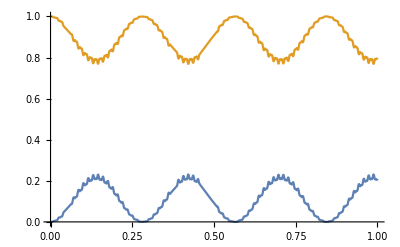

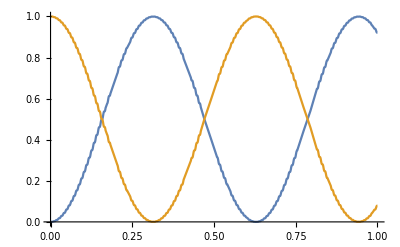

```mathematica
(*ReImPlot[Evaluate[{c0[t],c1[t]}/. results0],{t,0,T}]
ReImPlot[Evaluate[{c0[t],c1[t]}/. results1],{t,0,T}]*)
Plot[Evaluate[{c0[t]*Conjugate[c0[t]],c1[t]*Conjugate[c1[t]]}/. results0],{t,0,T}]
(*Die Lösung ist komplex. Berechne also auch die Erwartungswerte.*)
Plot[Evaluate[{c0[t]*Conjugate[c0[t]],c1[t]*Conjugate[c1[t]]}/. results1],{t,0,T}]
(*Überprüfe Erhaltungssatz*)
(*Plot[Evaluate[{c0[t]*Conjugate[c0[t]]+c1[t]*Conjugate[c1[t]]}/. results0],{t,0,T}]
Plot[Evaluate[{c0[t]*Conjugate[c0[t]]+c1[t]*Conjugate[c1[t]]}/. results1],{t,0,T}]*)
```

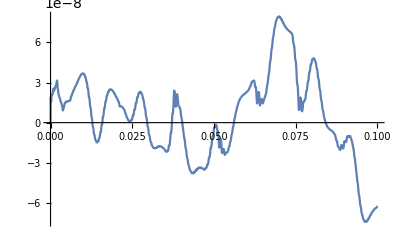

```mathematica
(*Check quality of numerical solution*)
lowsol=NDSolve[eqns0,vars,{t,0,T},InterpolationOrder->All];
highsol=NDSolve[eqns0,vars,{t,0,T},WorkingPrecision->22,InterpolationOrder->All];
Plot[Evaluate[Re[(c0[t]/. lowsol)-(c0[t]/. highsol)]],{t,0,T}]
(*Plot[Evaluate[RealExponent[(c0[t]/. lowsol)-(c0[t]/. highsol)]],{t,0,0.1}]*)
```

```mathematica
(*Weiteres Vorgehen: Überprüfen, ob die Lösung oben in RWA die Lösung ergibt, die ich hergeleitet hatte. Mir überlegen, warum die Gültigkeit der RWA von der gewählten Verstimmung abhängt. Benötige dafür genäherten Hamiltonian:*)
H0RWA=((ωL*Cos[β]-ω)*Cos[β]-Ω*Sin[β]*Cos[β]*Cos[ϕ])/2*PauliMatrix[3]+(-ω*Sin[β]+ωL*Cos[β]*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H1RWA=((ω1-ω)*Cos[β]-Ω*Cos[β]*Sin[β]*Cos[ϕ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
```

```mathematica
(*simple case: resonant driving, phase of drive is zero*)
H0RWAS=FullSimplify[H0RWA/.{ω->Sqrt[B^2+(ωL-A)^2],ϕ->0}] ;
H1RWAS=FullSimplify[H1RWA/.{ω->Sqrt[B^2+(ωL-A)^2],ϕ->0}];
```

```mathematica
H0RWAB=H0RWA/.{ω->-Ω*Sin[β]+ω1,ϕ->0};
H1RWAB=H1RWA/.{ω->-Ω*Sin[β]+ω1,ϕ->0};
H0RWAB=H0RWAB/.{Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H1RWAB=H1RWAB/.{Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
```

```mathematica
(*get differential equations from Hamiltonian. Start with H0*)
res0RWA= FullSimplify[-ⅈ*H0RWAS.psi];
res1RWA= FullSimplify[-ⅈ*H1RWAS.psi];
```

```mathematica
res0RWA=res0RWA/.{c0->c0[t],c1->c1[t]};
res1RWA=res1RWA/.{c0->c0[t],c1->c1[t]};
```

```mathematica
eqns0RWA={c0'[t]==res0RWA[[1]],
c1'[t]== res0RWA[[2]],c0[0]==c00,c1[0]==c10};
eqns1RWA={c0'[t]==res1RWA[[1]],
c1'[t]==res1RWA[[2]],c0[0]==c00,c1[0]==c10};
(*eqns0RWA=eqns0RWA/.{ω->Sqrt[B^2+(ωL-A)^2]} (*resonant driving, ω=ω1*)
eqns1RWA=eqns1RWA/.{ω->Sqrt[B^2+(ωL-A)^2]} (*resonant driving, ω=ω1*)*)
eqns0RWA=eqns0RWA/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue};
eqns1RWA=eqns1RWA/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue};
```

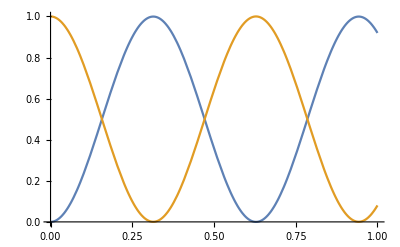

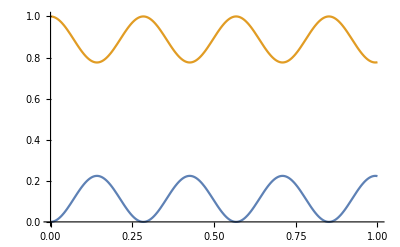

```mathematica
resultsRWA0=NDSolve[eqns0RWA,vars,{t,0,T}];
resultsRWA1=NDSolve[eqns1RWA,vars,{t,0,T}];
(*ReImPlot[Evaluate[{c0[t],c1[t]}/. resultsRWA0],{t,0,T}]
ReImPlot[Evaluate[{c0[t],c1[t]}/. resultsRWA1],{t,0,T}]*)
(*Die Lösung ist komplex. Berechne also auch die Erwartungswerte.*)
Plot[Evaluate[{c0[t]*Conjugate[c0[t]],c1[t]*Conjugate[c1[t]]}/.resultsRWA1],{t,0,T}]
Plot[Evaluate[{c0[t]*Conjugate[c0[t]],c1[t]*Conjugate[c1[t]]}/.resultsRWA0],{t,0,T}]
(*Überprüfe Erhaltungssatz*)
(*Plot[Evaluate[{c0[t]*Conjugate[c0[t]]+c1[t]*Conjugate[c1[t]]}/.resultsRWA0],{t,0,T}]
Plot[Evaluate[{c0[t]*Conjugate[c0[t]]+c1[t]*Conjugate[c1[t]]}/.resultsRWA1],{t,0,T}]*)
```

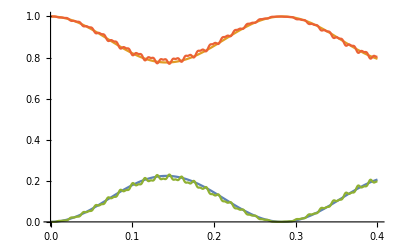

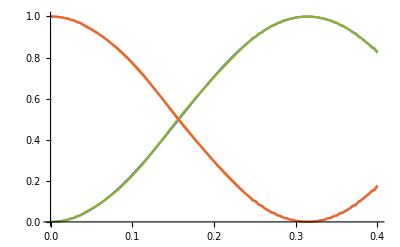

```mathematica
(*Compare results*)
Plot[{Evaluate[{c0[t]*Conjugate[c0[t]],c1[t]*Conjugate[c1[t]]}/. resultsRWA0],Evaluate[{c0[t]*Conjugate[c0[t]],c1[t]*Conjugate[c1[t]]}/. results0]},{t,0,0.4*T}]
Plot[{Evaluate[{c0[t]*Conjugate[c0[t]],c1[t]*Conjugate[c1[t]]}/. resultsRWA1],Evaluate[{c0[t]*Conjugate[c0[t]],c1[t]*Conjugate[c1[t]]}/. results1]},{t,0,0.4*T}]
```

```mathematica
(*******************************************************************************************************)
(*******************************************************************************************************)
```

```mathematica
Compute Fidelity of physical process. Compute time evolution operator by solving the Schrödinger equation in the Heisenberg picture
```

```mathematica
(*first look at Fidelity of a single point depending on different values for hyperfine tensor components and Larmor frequency, thus detuning. H0Tilde/H1Tilde include the variable driving frequency ω and ϕ, while H0TildeS/H1TileS are simplified versions including a resonant drive and ϕ equals 0.*)
Ucnot=({{-1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, -ⅈ}, {0, 0, -ⅈ, 0}}); (*CNOT up to single qubit rotations*)
ωLvalue = 430; (*exemplary values for typical regimes: 27 kHz, 430kHz, 1980 kHz*)
Avalue = 50;
Bvalue=10;
ϕvalue = 0;
t0=0;
Ωvalue=8;
(*Ωvalue=Avalue*Sqrt[1/3];*)
Ω0=Sqrt[(1/2 Cos[β] (-ω1+ωL Cos[β]))^2+(1/2 (Ω-ω1 Sin[β]+ωL Cos[β] Sin[β]))^2]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
tg1=(π*(2n+1))/Ω;
ΩvalueB=Solve[Ω0^2*tg1^2==π^2*m^2/.{A->Avalue,B->Bvalue,ωL->ωLvalue,n->0,m->1},Ω][[2]][[1]][[2]][[1]];
ω1value =Sqrt[Bvalue^2+(ωLvalue-Avalue)^2];
sinusbeta=Bvalue/Sqrt[Bvalue^2+(ωLvalue-Avalue)^2];
ωvalue = ω1value-sinusbeta*ΩvalueB;
tgB=π/ΩvalueB;
tg=π/Ωvalue;
u0=IdentityMatrix@Length@H0Tilde;
U0r=NDSolve[{-ⅈ*D[u[t],t]==(H0TildeS/.{A->Avalue,B->Bvalue, Ω->Ωvalue, ωL-> ωLvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
U1r=NDSolve[{-ⅈ*D[u[t],t]==(H1TildeS/.{ A->Avalue,B->Bvalue, Ω->Ωvalue,ωL-> ωLvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
U0f=NDSolve[{-ⅈ*D[u[t],t]==(H0TildeB/.{A->Avalue,B->Bvalue, Ω->ΩvalueB, ωL-> ωLvalue}).u[t],u[t0]==u0},u[t],{t,t0,tgB}][[1,1,2]]/.t->tgB;
U1f=NDSolve[{-ⅈ*D[u[t],t]==(H1TildeB/.{A->Avalue,B->Bvalue, Ω->ΩvalueB,ωL-> ωLvalue}).u[t],u[t0]==u0},u[t],{t,t0,tgB}][[1,1,2]]/.t->tgB;
Uact=KroneckerProduct[{{1,0},{0,0}},U0f]+KroneckerProduct[{{0,0},{0,1}},U1f];
Uactr=KroneckerProduct[{{1,0},{0,0}},U0r]+KroneckerProduct[{{0,0},{0,1}},U1r];
Uact//MatrixForm;

Favr=(Abs[Tr[Ucnot.Uactr]]^2+4)/20
(*N[tg*1000]*) (*gate time in microseconds*)

Fav=(Abs[Tr[Ucnot.Uact]]^2+4)/20
(*N[tgB*1000]*)(*gate time in microseconds*)
```

0.93206

0.998817

```mathematica
Now compute Fidelity of approximation (RWA) for a single point in parameter space in order to compare the quality of the approximation with the full solution.
```

```mathematica
u0=IdentityMatrix@Length@H0RWA;
U0RWA=IdentityMatrix@Length@H0Tilde;
U1RWA=IdentityMatrix@Length@H0Tilde;
U0RWAS=NDSolve[{-ⅈ*D[u[t],t]==(H0RWAS/.{ω->ωvalue, ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue,ϕ->ϕvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
U1RWAS=NDSolve[{-ⅈ*D[u[t],t]==(H1RWAS/.{ω->ωvalue, ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue,ϕ->ϕvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
U0RWA=NDSolve[{-ⅈ*D[u[t],t]==(H0RWAB/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->ΩvalueB}).u[t],u[t0]==u0},u[t],{t,t0,tgB}][[1,1,2]]/.t->tgB;
U1RWA=NDSolve[{-ⅈ*D[u[t],t]==(H1RWAB/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->ΩvalueB}).u[t],u[t0]==u0},u[t],{t,t0,tgB}][[1,1,2]]/.t->tgB;
UactRWA=KroneckerProduct[{{1,0},{0,0}},U0RWA]+KroneckerProduct[{{0,0},{0,1}},U1RWA];
UactRWAS=KroneckerProduct[{{1,0},{0,0}},U0RWAS]+KroneckerProduct[{{0,0},{0,1}},U1RWAS];
FavRWA=(Abs[Tr[Ucnot.UactRWA]]^2+4)/20
FavRWAS=(Abs[Tr[Ucnot.UactRWAS]]^2+4)/20
FavCompare=(Abs[Tr[ConjugateTranspose[Uact].UactRWA]]^2+4)/20
FavComparer=(Abs[Tr[ConjugateTranspose[Uactr].UactRWAS]]^2+4)/20
```

1.

0.917685

0.998817

0.998914

```mathematica
Reproduce plot of fidelity over driving strength for uncorrected gate, where I plug in the gate time giving a CNOT locally A_parallel*Sqrt[1/3].
```

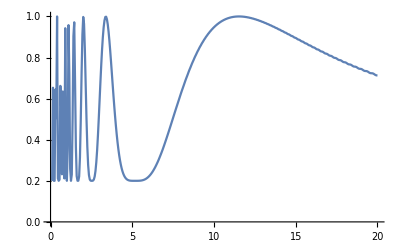

```mathematica
(*Create plot of Fidelity over Ω for full process, for approximated process and for a comparison between both*)
(*first for full process*)
u0=IdentityMatrix@Length@H0Tilde;
idlefidelitylist={};
For[i=1,i<400,i++;
U0=IdentityMatrix@Length@H0Tilde;
U1=IdentityMatrix@Length@H0Tilde;
(*insert gate time*)
Ωvalue=0.05*i;
tg=π/Ωvalue;
U0=NDSolve[{-ⅈ*D[u[t],t]==(H0TildeS/.{A->Avalue,B->Bvalue, Ω->Ωvalue, ωL-> ωLvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
U1=NDSolve[{-ⅈ*D[u[t],t]==(H1TildeS/.{A->Avalue,B->Bvalue, Ω->Ωvalue,ωL-> ωLvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
(*U0=NDSolve[{ⅈ*D[u[t],t]==(H0TildeS/.{ω1->Sqrt[B^2+(ωL-A)^2],ω->Sqrt[B^2+(ωL-A)^2]}/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
U1=NDSolve[{ⅈ*D[u[t],t]==(H1TildeS/.{ω1->Sqrt[B^2+(ωL-A)^2],ω->Sqrt[B^2+(ωL-A)^2]}/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;*)
Uact=KroneckerProduct[{{1,0},{0,0}},U0]+KroneckerProduct[{{0,0},{0,1}},U1];
AppendTo[idlefidelitylist,{Ωvalue,((Abs[Tr[Ucnot.Uact]]^2+4)/20)}];
]
ListLinePlot[{idlefidelitylist}]
```

```mathematica
Avalue
N[Avalue*Sqrt[1/3]]
Ωval=Avalue*Sqrt[1/3]-Avalue*0.05
```

20

11.547

10.547

```mathematica
Plot full solution to see if synchronization points exist for different values, so look fine-grained at a small interval around an synchronization point
```

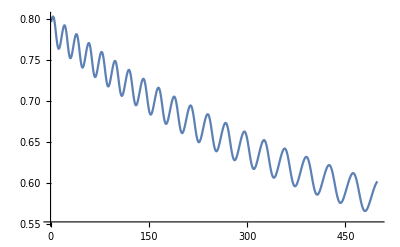

```mathematica
Ucnot=({{-1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, -ⅈ}, {0, 0, -ⅈ, 0}}); (*CNOT up to single qubit rotations*)
u0=IdentityMatrix@Length@H0Tilde;
idlefidelitylist={};
Ωval=Avalue*Sqrt[1/3]-Avalue*0.1;
For[i=1,i<500,i++;
U0=IdentityMatrix@Length@H0Tilde;
U1=IdentityMatrix@Length@H0Tilde;
(*insert gate time and driving strength*)
Ωvalue=Ωval+0.01*i;
tg=π/Ωvalue;
U0=NDSolve[{-ⅈ*D[u[t],t]==(H0TildeS/.{A->Avalue,B->Bvalue, Ω->Ωvalue, ωL-> ωLvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
U1=NDSolve[{-ⅈ*D[u[t],t]==(H1TildeS/.{A->Avalue,B->Bvalue, Ω->Ωvalue,ωL-> ωLvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
Uact=KroneckerProduct[{{1,0},{0,0}},U0]+KroneckerProduct[{{0,0},{0,1}},U1];
AppendTo[idlefidelitylist,((Abs[Tr[Ucnot.Uact]]^2+4)/20)];
]
ListLinePlot[idlefidelitylist]
```

```mathematica
(*Now compute Fidelity of approximation (RWA)*)
(*first check should be if we get the correct dynamics with the simple RWA version where Aperp is neglected*)
(*Hamiltonian:*)
Ucnot=({{-1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, -ⅈ}, {0, 0, -ⅈ, 0}}); (*CNOT up to single qubit rotations*)
H0check=((ωL*Cos[β]-ω)*Cos[β]-Ω*Sin[β]*Cos[β]*Cos[ϕ])/2*PauliMatrix[3]+(-ω*Sin[β]+ωL*Cos[β]*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A,ϕ->0};
H1check=((ω1-ω)*Cos[β]-Ω*Cos[β]*Sin[β]*Cos[ϕ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A,ϕ->0};
Hactcheck=KroneckerProduct[{{1,0},{0,0}},H0check]+KroneckerProduct[{{0,0},{0,1}},H1check];
```

```mathematica
(*Dynamics:*)
Uactcheck=KroneckerProduct[{{1,0},{0,0}},FullSimplify[MatrixExp[-I*H0check*t]/.t->π/Ω]]+KroneckerProduct[{{0,0},{0,1}},FullSimplify[MatrixExp[-I*H1check*t]/.t->π/Ω]]/.Ω->A*Sqrt[1/3];
Uactcheck=FullSimplify[Uactcheck];
Fav=(Abs[Tr[Ucnot.Uactcheck]]^2+4)/20
```

```mathematica
Avalue=3.03;
Ωvalue=Avalue*Sqrt[1/3];
tg=π/Ωvalue;
U0check=NDSolve[{-ⅈ*D[u[t],t]==(H0check/.{A->Avalue,Ω->Ωvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
U1check=NDSolve[{-ⅈ*D[u[t],t]==(H1check/.{A->Avalue,Ω->Ωvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
Uactcheck=KroneckerProduct[{{1,0},{0,0}},U0check]+KroneckerProduct[{{0,0},{0,1}},U1check];
Uactcheck//MatrixForm

Fav=(Abs[Tr[Ucnot.Uactcheck]]^2+4)/20
```

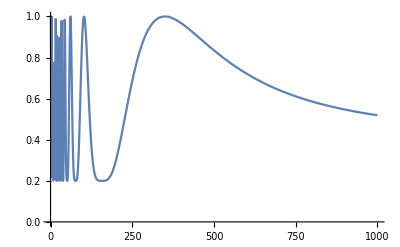

```mathematica
u0=IdentityMatrix@Length@H0check;
idlefidelitylist={};
Avalue=3.03;
For[i=0,i<1000,i++;
(*insert gate time*)
Ωvalue=0.005*i;
tg=π/Ωvalue;
U0check=NDSolve[{-ⅈ*D[u[t],t]==(H0check/.{A->Avalue,Ω->Ωvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
U1check=NDSolve[{-ⅈ*D[u[t],t]==(H1check/.{A->Avalue,Ω->Ωvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
Uactcheck=KroneckerProduct[{{1,0},{0,0}},U0check]+KroneckerProduct[{{0,0},{0,1}},U1check];
AppendTo[idlefidelitylist,((Abs[Tr[Ucnot.Uactcheck]]^2+4)/20)];
]
ListLinePlot[idlefidelitylist]
```

```mathematica
(*Now compute Fidelity of approximation (RWA)*)
(*first check should be if we get the correct dynamics with B=0 and with/without off-resonant drive*)
u0=IdentityMatrix@Length@H0RWA;
idlefidelitylist={};
Avalue=3.03;
For[i=0,i<1000,i++;
U0RWA=IdentityMatrix@Length@H0Tilde;
U1RWA=IdentityMatrix@Length@H0Tilde;
(*insert gate time*)
Ωvalue=0.005*i;
tg=π/Ωvalue;
U0RWA=NDSolve[{-ⅈ*D[u[t],t]==(H0RWA/.{ω1->Sqrt[B^2+(ωL-A)^2],ω->Sqrt[B^2+(ωL-A)^2]}/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
U1RWA=NDSolve[{-ⅈ*D[u[t],t]==(H1RWA/.{ω1->Sqrt[B^2+(ωL-A)^2],ω->Sqrt[B^2+(ωL-A)^2]}/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue}).u[t],u[t0]==u0},u[t],{t,t0,tg}][[1,1,2]]/.t->tg;
UactRWA=KroneckerProduct[{{1,0},{0,0}},U0RWA]+KroneckerProduct[{{0,0},{0,1}},U1RWA];
AppendTo[idlefidelitylist,((Abs[Tr[Ucnot.UactRWA]]^2+4)/20)];
]
ListLinePlot[idlefidelitylist]
```

-Graphics-

```mathematica
(*******************************************************************************************************)
(*******************************************************************************************************)
```

```mathematica
(*******************************************************************************************************)
(*This way of defining the hamiltonian in the rotating frame is identical to the transformation above I just tried it for the different output Mathematica gives*)
Hd0=Ω*Cos[ω*t +ϕ]*PauliMatrix[1];
H00=ωL/2*PauliMatrix[3];
Hd1 = Ω*Cos[β]*Cos[ω*t +ϕ]*(Cos[β]*PauliMatrix[1]-Sin[β]*PauliMatrix[3])+Ω*Sin[β]*Cos[ω*t +ϕ]*(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3]);
H10=ω1/2*(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3]);

Hd0Tilde0=FullSimplify[U.Hd0.UDag];
H00Tilde0=FullSimplify[U.H00.UDag];
Hd1Tilde0=FullSimplify[U.Hd1.UDag];
H10Tilde0=FullSimplify[U.H10.UDag];
H0TildeN=H00Tilde0-ω/2(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])+Hd0Tilde0;
H1TildeN=H10Tilde0-ω/2(Sin[β]*PauliMatrix[1]+Cos[β]*PauliMatrix[3])+Hd1Tilde0;
H0TildeN//MatrixForm
H1TildeN//MatrixForm
(*******************************************************************************************************)
```

(-1/2 ω Cos[β]+1/2 ωL (Cos[β]^2+Cos[t ω] Sin[β]^2)+Ω Cos[ϕ+t ω] Sin[2 β] Sin[(t ω)/2]^2 | -1/2 ω Sin[β]-1/2 ωL Sin[β] (Cos[β] (-1+Cos[t ω])+ⅈ Sin[t ω])+1/2 Ω Cos[ϕ+t ω] (1+Cos[β]^2 (-1+2 Cos[t ω])+Sin[β]^2+2 ⅈ Cos[β] Sin[t ω])
-1/2 ω Sin[β]+ωL Sin[β] Sin[(t ω)/2] (ⅈ Cos[(t ω)/2]+Cos[β] Sin[(t ω)/2])+1/2 Ω Cos[ϕ+t ω] (1+Cos[β]^2 (-1+2 Cos[t ω])+Sin[β]^2-2 ⅈ Cos[β] Sin[t ω]) | 1/2 ω Cos[β]-1/2 ωL (Cos[β]^2+Cos[t ω] Sin[β]^2)-Ω Cos[ϕ+t ω] Sin[2 β] Sin[(t ω)/2]^2)

(-1/2 ω Cos[β]+1/2 ω1 Cos[β]+Ω Cos[ϕ+t ω] Sin[2 β] Sin[(t ω)/2]^2 | -1/2 ω Sin[β]+1/2 ω1 Sin[β]+1/2 Ω Cos[ϕ+t ω] (1+Cos[β]^2 (-1+2 Cos[t ω])+Sin[β]^2+2 ⅈ Cos[β] Sin[t ω])
-1/2 ω Sin[β]+1/2 ω1 Sin[β]+1/2 Ω Cos[ϕ+t ω] (1+Cos[β]^2 (-1+2 Cos[t ω])+Sin[β]^2-2 ⅈ Cos[β] Sin[t ω]) | 1/2 ω Cos[β]-1/2 ω1 Cos[β]-Ω Cos[ϕ+t ω] Sin[2 β] Sin[(t ω)/2]^2)

```mathematica
(*******************************************************************************************************)
(*Check numerical integration with known solution*)
H0check=((ωL*Cos[β]-ω)*Cos[β]-Ω*Sin[β]*Cos[β]*Cos[ϕ])/2*PauliMatrix[3]+(-ω*Sin[β]+ωL*Cos[β]*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A};
H1check=((ω1-ω)*Cos[β]-Ω*Cos[β]*Sin[β]*Cos[ϕ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A};
H0check //MatrixForm
H1check //MatrixForm

({{A/2, 1/2 Ω Cos[ϕ]-1/2 ⅈ Ω Sin[ϕ]}, {1/2 Ω Cos[ϕ]+1/2 ⅈ Ω Sin[ϕ], -A/2}})
({{0, 1/2 Ω Cos[ϕ]-1/2 ⅈ Ω Sin[ϕ]}, {1/2 Ω Cos[ϕ]+1/2 ⅈ Ω Sin[ϕ], 0}})
(*get differential equations from Hamiltonian. Start with H0*)
psi={c0,c1};
res0= FullSimplify[-ⅈ*H0check.psi];
res1= FullSimplify[-ⅈ*H1check.psi];
res1=res1/.{c0->c0[t],c1->c1[t]}
res0=res0/.{c0->c0[t],c1->c1[t]}
{-1/2 ⅈ ⅇ^(-ⅈ ϕ) Ω c1[t],1/2 Ω c0[t] (-ⅈ Cos[ϕ]+Sin[ϕ])}
{-1/2 ⅈ (A c0[t]+ⅇ^(-ⅈ ϕ) Ω c1[t]),1/2 ⅈ (-ⅇ^(ⅈ ϕ) Ω c0[t]+A c1[t])}
eqns0={c0'[t]==res0[[1]],
c1'[t]== res0[[2]],c0[0]==0,c1[0]==1};
eqns1={c0'[t]==res1[[1]],
c1'[t]==res1[[2]],c0[0]==0,c1[0]==1 };
vars={c0[t],c1[t]};
eqns0=eqns0/.{ω1->Sqrt[B^2+(ωL-A)^2],ω->Sqrt[B^2+(ωL-A)^2]}; (*resonant driving, ω=ω1*)
eqns1=eqns1/.{ω1->Sqrt[B^2+(ωL-A)^2],ω->Sqrt[B^2+(ωL-A)^2]}; (*resonant driving, ω=ω1*)
eqns0=eqns0/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue};
eqns1=eqns1/.{ϕ->ϕvalue,A->Avalue,B->Bvalue,ωL->ωLvalue,Ω->Ωvalue};
results0=NDSolve[eqns0,vars,{t,0,T}];
results1=NDSolve[eqns1,vars,{t,0,T}];

ReImPlot[Evaluate[{c0[t],c1[t]}/. results0],{t,0,T}]
ReImPlot[Evaluate[{c0[t],c1[t]}/. results1],{t,0,T}]
Plot[Evaluate[{Sqrt[c0[t]*Conjugate[c0[t]]],Sqrt[c1[t]*Conjugate[c1[t]]]}/. results0],{t,0,T}]
Plot[Evaluate[{Sqrt[c0[t]*Conjugate[c0[t]]],Sqrt[c1[t]*Conjugate[c1[t]]]}/. results1],{t,0,T}]
```